# An Elementary Introduction to Wolfram Language

## Part 4

## 部分列表

```mathematica
list={a,b,c,d,e,f};
```

取出第4个

```mathematica
Part[list,4]
```

d

取出前4个

```mathematica
Take[list,4]
```

{a,b,c,d}

丢弃前4个

```mathematica
Drop[list,4]
```

{e,f}

取出倒数第2个

```mathematica
Part[list,-2]
```

e

取出最后2个

```mathematica
Take[list,-2]
```

{e,f}

丢弃最后2个

```mathematica
Drop[list,-2]
```

{a,b,c,d}

```mathematica
table={{a,b,c},{d,e,f},{g,h,i}};
```

取出第一列

```mathematica
table[[All,1]]
```

{a,d,g}

给出元素所在坐标

```mathematica
Position[table,d]
```

{{2,1}}

```mathematica
Position[Characters["Hello world!"],"l"]
```

{{3},{4},{10}}

找出生日在Pi中的位置

```mathematica
PiString=StringDrop[ToString@N[Pi,10^7],{2}];
```

```mathematica
First@StringPosition[PiString,"0033"]
```

{6219,6222}

字母e在单词中出现的位置

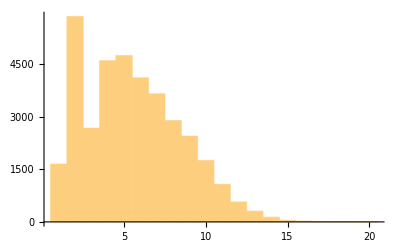

```mathematica
Position[Characters@#,"e"]&/@WordList[Language->"English"]//Flatten//Histogram
```

替换列表中元素

```mathematica
ReplacePart[list,{3->x,5->y}]
```

{a,b,x,d,y,f}

并不改动原列表

```mathematica
list
```

{a,b,c,d,e,f}

元素改为Nothing，相当于删除对应元素

```mathematica
ReplacePart[list,{3->Nothing,5->Nothing}]
```

{a,b,d,f}

取最大数

```mathematica
TakeLargest[Range[20],5]
```

{20,19,18,17,16}

取最长罗马数字

```mathematica
TakeLargestBy[Array[RomanNumeral,100],StringLength,5]
```

{LXXXVIII,LXXXIII,XXXVIII,LXXVIII,LXXXVII}

## 模式

找出1开头9结尾的列表

```mathematica
Cases[IntegerDigits@Range@1000,{1,__,9}]
```

{{1,0,9},{1,1,9},{1,2,9},{1,3,9},{1,4,9},{1,5,9},{1,6,9},{1,7,9},{1,8,9},{1,9,9}}

找出3个相同元素的列表

```mathematica
Cases[IntegerDigits@Range@1000,{x_,x_,x_}]
```

{{1,1,1},{2,2,2},{3,3,3},{4,4,4},{5,5,5},{6,6,6},{7,7,7},{8,8,8},{9,9,9}}

前一千个平方数里，9开头、0或1结尾

```mathematica
Cases[IntegerDigits@Power[Range@1000,2],{9,__,0|1}]
```

{{9,0,0},{9,6,1},{9,8,0,1},{9,0,0,0,0},{9,0,6,0,1},{9,5,4,8,1},{9,6,1,0,0},{9,6,7,2,1},{9,0,0,6,0,1},{9,0,2,5,0,0},{9,0,4,4,0,1},{9,1,9,6,8,1},{9,2,1,6,0,0},{9,2,3,5,2,1},{9,3,8,9,6,1},{9,4,0,9,0,0},{9,4,2,8,4,1},{9,5,8,4,4,1},{9,6,0,4,0,0},{9,6,2,3,6,1},{9,7,8,1,2,1},{9,8,0,1,0,0},{9,8,2,0,8,1},{9,9,8,0,0,1}}

替换

```mathematica
IntegerDigits@Range@100/.{0->Gray,9->Orange}
```

{{1},{2},{3},{4},{5},{6},{7},{8},{RGBColor[1, 0.5, 0]},{1,GrayLevel[0.5]},{1,1},{1,2},{1,3},{1,4},{1,5},{1,6},{1,7},{1,8},{1,RGBColor[1, 0.5, 0]},{2,GrayLevel[0.5]},{2,1},{2,2},{2,3},{2,4},{2,5},{2,6},{2,7},{2,8},{2,RGBColor[1, 0.5, 0]},{3,GrayLevel[0.5]},{3,1},{3,2},{3,3},{3,4},{3,5},{3,6},{3,7},{3,8},{3,RGBColor[1, 0.5, 0]},{4,GrayLevel[0.5]},{4,1},{4,2},{4,3},{4,4},{4,5},{4,6},{4,7},{4,8},{4,RGBColor[1, 0.5, 0]},{5,GrayLevel[0.5]},{5,1},{5,2},{5,3},{5,4},{5,5},{5,6},{5,7},{5,8},{5,RGBColor[1, 0.5, 0]},{6,GrayLevel[0.5]},{6,1},{6,2},{6,3},{6,4},{6,5},{6,6},{6,7},{6,8},{6,RGBColor[1, 0.5, 0]},{7,GrayLevel[0.5]},{7,1},{7,2},{7,3},{7,4},{7,5},{7,6},{7,7},{7,8},{7,RGBColor[1, 0.5, 0]},{8,GrayLevel[0.5]},{8,1},{8,2},{8,3},{8,4},{8,5},{8,6},{8,7},{8,8},{8,RGBColor[1, 0.5, 0]},{RGBColor[1, 0.5, 0],GrayLevel[0.5]},{RGBColor[1, 0.5, 0],1},{RGBColor[1, 0.5, 0],2},{RGBColor[1, 0.5, 0],3},{RGBColor[1, 0.5, 0],4},{RGBColor[1, 0.5, 0],5},{RGBColor[1, 0.5, 0],6},{RGBColor[1, 0.5, 0],7},{RGBColor[1, 0.5, 0],8},{RGBColor[1, 0.5, 0],RGBColor[1, 0.5, 0]},{1,GrayLevel[0.5],GrayLevel[0.5]}}

/. 0 需要多一个空格，否则与除法混淆

```mathematica
IntegerDigits[2^1000]/. 0->Red
```

{1,RGBColor[1, 0, 0],7,1,5,RGBColor[1, 0, 0],8,6,RGBColor[1, 0, 0],7,1,8,6,2,6,7,3,2,RGBColor[1, 0, 0],9,4,8,4,2,5,RGBColor[1, 0, 0],4,9,RGBColor[1, 0, 0],6,RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],1,8,1,RGBColor[1, 0, 0],5,6,1,4,RGBColor[1, 0, 0],4,8,1,1,7,RGBColor[1, 0, 0],5,5,3,3,6,RGBColor[1, 0, 0],7,4,4,3,7,5,RGBColor[1, 0, 0],3,8,8,3,7,RGBColor[1, 0, 0],3,5,1,RGBColor[1, 0, 0],5,1,1,2,4,9,3,6,1,2,2,4,9,3,1,9,8,3,7,8,8,1,5,6,9,5,8,5,8,1,2,7,5,9,4,6,7,2,9,1,7,5,5,3,1,4,6,8,2,5,1,8,7,1,4,5,2,8,5,6,9,2,3,1,4,RGBColor[1, 0, 0],4,3,5,9,8,4,5,7,7,5,7,4,6,9,8,5,7,4,8,RGBColor[1, 0, 0],3,9,3,4,5,6,7,7,7,4,8,2,4,2,3,RGBColor[1, 0, 0],9,8,5,4,2,1,RGBColor[1, 0, 0],7,4,6,RGBColor[1, 0, 0],5,RGBColor[1, 0, 0],6,2,3,7,1,1,4,1,8,7,7,9,5,4,1,8,2,1,5,3,RGBColor[1, 0, 0],4,6,4,7,4,9,8,3,5,8,1,9,4,1,2,6,7,3,9,8,7,6,7,5,5,9,1,6,5,5,4,3,9,4,6,RGBColor[1, 0, 0],7,7,RGBColor[1, 0, 0],6,2,9,1,4,5,7,1,1,9,6,4,7,7,6,8,6,5,4,2,1,6,7,6,6,RGBColor[1, 0, 0],4,2,9,8,3,1,6,5,2,6,2,4,3,8,6,8,3,7,2,RGBColor[1, 0, 0],5,6,6,8,RGBColor[1, 0, 0],6,9,3,7,6}

删除匹配元素

```mathematica
DeleteCases[Characters["The Wolfram Language"],x_/;MemberQ[{"a","e","i","o","u"},x]]
```

{T,h, ,W,l,f,r,m, ,L,n,g,g}

同义代码

```mathematica
Select[IntegerDigits[2^1000],#==0||#==1&]
```

{1,0,1,0,0,1,0,0,0,0,0,0,1,1,0,1,0,1,1,0,0,0,0,1,0,1,1,1,1,1,1,1,1,1,1,1,0,0,0,1,0,0,0,1,1,1,1,1,0,1,1,1,0,0,1,1,1,1,0,1,0,0}

```mathematica
Cases[IntegerDigits[2^1000],0|1]
```

{1,0,1,0,0,1,0,0,0,0,0,0,1,1,0,1,0,1,1,0,0,0,0,1,0,1,1,1,1,1,1,1,1,1,1,1,0,0,0,1,0,0,0,1,1,1,1,1,0,1,1,1,0,0,1,1,1,1,0,1,0,0}

```mathematica
Select[IntegerDigits[Range[100,999]],First[#]==Last[#]&]
```

{{1,0,1},{1,1,1},{1,2,1},{1,3,1},{1,4,1},{1,5,1},{1,6,1},{1,7,1},{1,8,1},{1,9,1},{2,0,2},{2,1,2},{2,2,2},{2,3,2},{2,4,2},{2,5,2},{2,6,2},{2,7,2},{2,8,2},{2,9,2},{3,0,3},{3,1,3},{3,2,3},{3,3,3},{3,4,3},{3,5,3},{3,6,3},{3,7,3},{3,8,3},{3,9,3},{4,0,4},{4,1,4},{4,2,4},{4,3,4},{4,4,4},{4,5,4},{4,6,4},{4,7,4},{4,8,4},{4,9,4},{5,0,5},{5,1,5},{5,2,5},{5,3,5},{5,4,5},{5,5,5},{5,6,5},{5,7,5},{5,8,5},{5,9,5},{6,0,6},{6,1,6},{6,2,6},{6,3,6},{6,4,6},{6,5,6},{6,6,6},{6,7,6},{6,8,6},{6,9,6},{7,0,7},{7,1,7},{7,2,7},{7,3,7},{7,4,7},{7,5,7},{7,6,7},{7,7,7},{7,8,7},{7,9,7},{8,0,8},{8,1,8},{8,2,8},{8,3,8},{8,4,8},{8,5,8},{8,6,8},{8,7,8},{8,8,8},{8,9,8},{9,0,9},{9,1,9},{9,2,9},{9,3,9},{9,4,9},{9,5,9},{9,6,9},{9,7,9},{9,8,9},{9,9,9}}

```mathematica
Cases[IntegerDigits[Range[100,999]],{x_,__,x_}]
```

{{1,0,1},{1,1,1},{1,2,1},{1,3,1},{1,4,1},{1,5,1},{1,6,1},{1,7,1},{1,8,1},{1,9,1},{2,0,2},{2,1,2},{2,2,2},{2,3,2},{2,4,2},{2,5,2},{2,6,2},{2,7,2},{2,8,2},{2,9,2},{3,0,3},{3,1,3},{3,2,3},{3,3,3},{3,4,3},{3,5,3},{3,6,3},{3,7,3},{3,8,3},{3,9,3},{4,0,4},{4,1,4},{4,2,4},{4,3,4},{4,4,4},{4,5,4},{4,6,4},{4,7,4},{4,8,4},{4,9,4},{5,0,5},{5,1,5},{5,2,5},{5,3,5},{5,4,5},{5,5,5},{5,6,5},{5,7,5},{5,8,5},{5,9,5},{6,0,6},{6,1,6},{6,2,6},{6,3,6},{6,4,6},{6,5,6},{6,6,6},{6,7,6},{6,8,6},{6,9,6},{7,0,7},{7,1,7},{7,2,7},{7,3,7},{7,4,7},{7,5,7},{7,6,7},{7,7,7},{7,8,7},{7,9,7},{8,0,8},{8,1,8},{8,2,8},{8,3,8},{8,4,8},{8,5,8},{8,6,8},{8,7,8},{8,8,8},{8,9,8},{9,0,9},{9,1,9},{9,2,9},{9,3,9},{9,4,9},{9,5,9},{9,6,9},{9,7,9},{9,8,9},{9,9,9}}

## 表达式及其结构

树结构

```mathematica
ExpressionTree[{f[x,f[x,y]],{x,y,f[1]}}]
```

-Graphics-

```mathematica
LeafCount[{f[x,f[x,y]],{x,y,f[1]}}]
```

11

```mathematica
ByteCount[{f[x,f[x,y]],{x,y,f[1]}}]
```

296

```mathematica
ExpressionTree[Graphics[{Circle[{0,0}],Hue[0.5],Disk[{1,1}]}]]
```

-Graphics-

```mathematica
LeafCount[Graphics[{Circle[{0,0}],Hue[0.5],Disk[{1,1}]}]]
```

12

```mathematica
ByteCount[Graphics[{Circle[{0,0}],Hue[0.5],Disk[{1,1}]}]]
```

448

提取圆的坐标

```mathematica
Graphics[Circle[{0,0}]][[1,1]]
```

{0,0}

标头

```mathematica
Head/@{1234,12.45,"hello",x}
```

{Integer,Real,String,Symbol}

用标头模式匹配

```mathematica
Cases[{x,y,3,4,z,6,7},_Integer]
```

{3,4,6,7}

纯函数的完全格式

```mathematica
FullForm[#^2&]
```

Function[Power[Slot[1],2]]

用 Length 统计参数个数

```mathematica
Length@f[x,y,z]
```

3

语法糖

```mathematica
f/@g[x,y,z]
```

g[f[x],f[y],f[z]]

```mathematica
f@@{x,y,z}
```

f[x,y,z]

```mathematica
f@@@{{1,2,3},{4,5,6}}
```

{f[1,2,3],f[4,5,6]}

计算阶乘

```mathematica
Times@@Range@100
```

93326215443944152681699238856266700490715968264381621468592963895217599993229915608941463976156518286253697920827223758251185210916864000000000000000000000000

```mathematica
100!
```

93326215443944152681699238856266700490715968264381621468592963895217599993229915608941463976156518286253697920827223758251185210916864000000000000000000000000

字母传递图

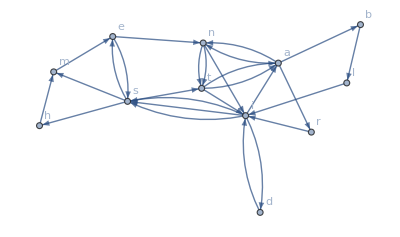

```mathematica
Graph[Rule@@@Partition[Characters["antidisestablishmentarianism"],2,1],VertexLabels->All]
```

## 关联

```mathematica
counts=Counts[{a,a,b,c,a,a,b,c,c,a,a}]
```

<|a→6,b→2,c→3|>

```mathematica
counts[c]
```

3

```mathematica
counts+500
```

<|a→506,b→502,c→503|>

```mathematica
f/@counts
```

<|a→f[6],b→f[2],c→f[3]|>

```mathematica
Total@counts
```

11

排序

```mathematica
Sort@counts
```

<|b→2,c→3,a→6|>

```mathematica
KeySort@counts
```

<|a→6,b→2,c→3|>

取出键值

```mathematica
{Keys@counts,Values@counts}
```

{{a,b,c},{6,2,3}}

转换为普通列表

```mathematica
Normal@counts
```

{a→6,b→2,c→3}

反向操作

```mathematica
Association@%
```

<|a→6,b→2,c→3|>

字母统计

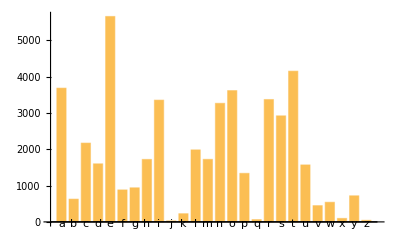

```mathematica
BarChart[KeyTake[LetterCounts[WikipediaData["computers"]],Alphabet[]],ChartLabels->Automatic]
```

文章中字母e的比例

```mathematica
#e/Total[#]&@LetterCounts[WikipediaData["computers"]]//N
```

0.117128

## 自然语言理解

```mathematica
Interpreter["CurrencyAmount"][{"4.25 dollars","85 cents","3400 rupees","5 euros"}]
```

{4.25 $,85 ¢,3400 ₹,5 €}

按当前汇率计算

```mathematica
Total@%
```

50.45 $

地理位置

```mathematica
Interpreter["Location"]["White House"]
```

GeoPosition[{38.8977,-77.0366}]

动物图像

```mathematica
EntityValue[Interpreter["Animal"][{"cheetah","tiger","elephant"}],"Image"]
```

{-Graphics-,-Graphics-,-Graphics-}

文本提取

```mathematica
TextCases["A sentence is a linguistic construct","Noun"]
```

{sentence,construct}

```mathematica
TextCases["Choose between $5, €5 and ¥5000","CurrencyAmount"]
```

{$5,€5,¥5000}

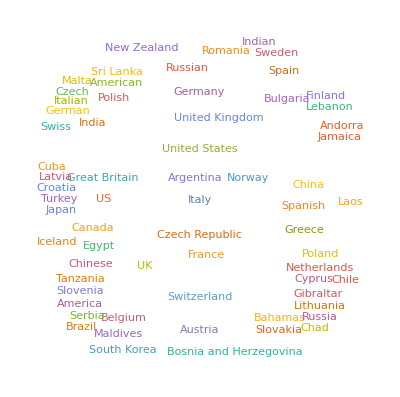

```mathematica
WordCloud[TextCases[WikipediaData["tourism"],"Country"]]
```

语法结构

```mathematica
TextStructure["You can do so much with the Wolfram Language."]
```

You
Pronoun
Noun Phrase  can
Verb  do
Verb  so
Adverbmuch
Adverb
Adverb Phrase  with
Preposition  the
DeterminerWolfram
Proper NounLanguage
Proper Noun
Noun Phrase
Prepositional Phrase
Verb Phrase
Verb Phrase.
Punctuation
Sentence

```mathematica
TextStructure["You can do so much with the Wolfram Language.", \
"ConstituentGraphs"]
```

{-Graphics-}

查字典

```mathematica
WordDefinition["computer"]
```

{a machine for performing calculations automatically,an expert at calculation (or at operating calculating machines)}

## 创建网站和应用程序

生成UUID

```mathematica
CloudPublish[GeoGraphics[GeoRange->All,GeoProjection->"Albers"]]
```

CloudObject[https://www.wolframcloud.com/obj/a0ecc139-71e5-44f1-9bf0-33fa43c1d91c]

短链接

```mathematica
URLShorten@CloudPublish[GeoGraphics[GeoRange->All,GeoProjection->"Albers"]]
```

https://wolfr.am/1rxn6mvU1

交互式内容，但是挺慢

```mathematica
CloudPublish[Manipulate[Graphics[Table[Circle[{0,0},r],{r,min,max}]],{min,1,30,1},{max,1,30,1}]]
```

CloudObject[https://www.wolframcloud.com/obj/ea405285-3795-4d8c-ab50-af28239f60c3]

## 布局和显示

加边框

```mathematica
Framed[2^100,Background->LightYellow,FrameStyle->LightGray]
```

1267650600228229401496703205376

加批注

```mathematica
Labeled[Style[2^100,Background->Yellow],Style["a big number",Italic,Orange]]
```

1267650600228229401496703205376a big number

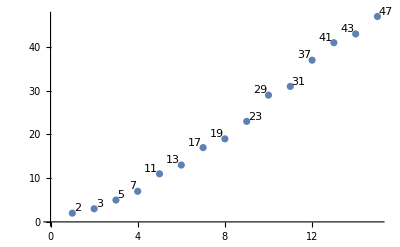

```mathematica
ListPlot[Table[Labeled[Prime[n],Prime[n]],{n,15}]]
```

```mathematica
ListPlot[Table[Callout[Prime[n],Prime[n]],{n,15}]]
```

-Graphics-

```mathematica
GraphicsGrid[Table[PieChart[RandomReal[10,5]],3,6],Frame->All]
```

-Graphics-

## 命名

局部参数

```mathematica
Module[{x=Range[10]},x^2]
```

{1,4,9,16,25,36,49,64,81,100}

过程式编程

```mathematica
Module[{x,y},x=Range[10];y=x^2;y=y+10000]
```

{10001,10004,10009,10016,10025,10036,10049,10064,10081,10100}

有初值的局部参数

```mathematica
Module[{x,y,n=2},x=Range[10];y=x^n;y=y+10000]
```

{10001,10004,10009,10016,10025,10036,10049,10064,10081,10100}

## 立即赋值和延迟赋值

区别

```mathematica
value=RandomColor[]
```

RGBColor[0.7848314745443963, 0.04045163504718774, 0.5314685057048358]

```mathematica
Table[value,10]
```

{RGBColor[0.7848314745443963, 0.04045163504718774, 0.5314685057048358],RGBColor[0.7848314745443963, 0.04045163504718774, 0.5314685057048358],RGBColor[0.7848314745443963, 0.04045163504718774, 0.5314685057048358],RGBColor[0.7848314745443963, 0.04045163504718774, 0.5314685057048358],RGBColor[0.7848314745443963, 0.04045163504718774, 0.5314685057048358],RGBColor[0.7848314745443963, 0.04045163504718774, 0.5314685057048358],RGBColor[0.7848314745443963, 0.04045163504718774, 0.5314685057048358],RGBColor[0.7848314745443963, 0.04045163504718774, 0.5314685057048358],RGBColor[0.7848314745443963, 0.04045163504718774, 0.5314685057048358],RGBColor[0.7848314745443963, 0.04045163504718774, 0.5314685057048358]}

```mathematica
value:=RandomColor[]
```

```mathematica
Table[value,10]
```

{RGBColor[0.5901874120060473, 0.26781311254344486, 0.13871749246039533],RGBColor[0.6255680922202091, 0.17092797585709896, 0.5558524123993585],RGBColor[0.0023523677929770948, 0.3346034611719937, 0.6535922371416616],RGBColor[0.5661865017314245, 0.30001075866092886, 0.18974880819417628],RGBColor[0.7209208454307274, 0.923798099400464, 0.732484407922658],RGBColor[0.8665027302273607, 0.9265096161536956, 0.8262575547797817],RGBColor[0.626919918763138, 0.9094248456725544, 0.9456843112619371],RGBColor[0.3633570718488597, 0.8511928962615323, 0.0975964674789429],RGBColor[0.7635093039390046, 0.655942522937744, 0.33126449800631974],RGBColor[0.8552187624052994, 0.6775483001574472, 0.12804494415877943]}

在n不确定时延迟赋值

```mathematica
circles:=Graphics[Table[Circle[{x,0},x/2],{x,n}]]
```

```mathematica
n=10
```

10

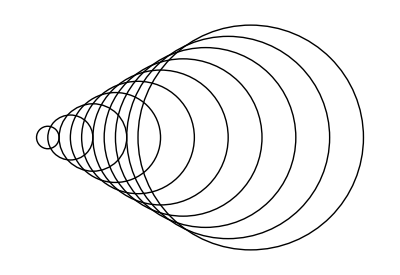

```mathematica
circles
```

延迟计算规则

```mathematica
x->RandomReal[]
```

x→0.521759

```mathematica
{x,x,x,x}/. x->RandomReal[]
```

{0.869787,0.869787,0.869787,0.869787}

```mathematica
x:>RandomReal[]
```

x:>RandomReal[]

```mathematica
{x,x,x,x}/. x:>RandomReal[]
```

{0.759115,0.65424,0.27742,0.728468}

## 自定义函数

定义函数

```mathematica
f[x_]:=Framed@Column[{x,ColorNegate@x}]
```

```mathematica
f/@{Red,Blue,Green}
```

{RGBColor[1, 0, 0]
RGBColor[0., 1., 1.],RGBColor[0, 0, 1]
RGBColor[1., 1., 0.],RGBColor[0, 1, 0]
RGBColor[1., 0., 1.]}

递归定义

```mathematica
factorial[1]=1;
factorial[n_Integer]:=n factorial[n-1]
```

```mathematica
factorial[50]//RepeatedTiming
```

{0.0000478646,30414093201713378043612608166064768844377641568960512000000000000}

用 If 定义

```mathematica
factorial[n_Integer]:=If[n==1,1,n factorial[n-1]]
```

```mathematica
factorial[50]//RepeatedTiming
```

{0.0000716541,30414093201713378043612608166064768844377641568960512000000000000}

内置函数

```mathematica
50!//RepeatedTiming
```

{1.00144×10^-7,30414093201713378043612608166064768844377641568960512000000000000}

作用于特定对象的函数

```mathematica
highlight[Framed[x_]]:=Style[Labeled[x,"+"],20,Background->LightYellow]
```

```mathematica
highlight/@{a,Framed[b],c,Framed[{10,20}],100}
```

{highlight[a],b+,highlight[c],{10,20}+,highlight[100]}

加一个定义，使之直接作用于列表

```mathematica
highlight[list_List]:=highlight/@list
```

```mathematica
highlight[{a,Framed[b],c,Framed[{10,20}],100}]
```

{highlight[a],b+,highlight[c],{10,20}+,highlight[100]}

再加一个定义

```mathematica
highlight[x_]:=Style[Rotate[x,-30 Degree],20,Orange]
```

```mathematica
highlight[{a,Framed[b],c,Framed[{10,20}],100}]
```

{a,b+,c,{10,20}+,100}